```mathematica
Quit[];
```

# A tutorial to use QuantumManyBody package

This notebook has to be considered as a tutorial, which will explain how to use the QuantumManyBody package to perform numerical computations. The package can be useful to simulate quantum mechanical systems in 1 dimension; such as spin chain models (having, say, L, spin sites) and the so-called SYK model, which is a strongly interacting model of N Majorana fermions, which will be included and discussed at length in a dedicated section.

First of all, let us load the package:

```mathematica
Needs["QuantumManyBody`"]
```

and we will focus first on showing functionalities which can be used to generate spin chain Hamiltonians (although, the vast majority of the functions can be used for Majorana Hamiltonians too). For simplicity, we will consider chains having 10 sites, which are then associated to Hilbert spaces of dimension 2^10

```mathematica
latticeSize = 10;
length = 2^latticeSize;
```

## Creating spin chain Hamiltonians using SpinChainHamiltonian and SpinOperators

The first function we want to address is the function SpinChainHamiltonian[listCouplings , listCoefficients]. Most of the Hamiltonians used in condensed matter are built out of lattices (defined on graphs) in which the spin variables (that here we call σ_i^a, with i being the site on the graph and a = x, y, z being the orientation of the spin along the 3 axes) interact through scalar products when they are connected by an edge of the underlying graph.

We will see through some examples, which kind of Hamiltonians can be generated and how.

## The Heisenberg model example

To start with, we will consider probably the simplest yet non-trivial example of Hamiltonian: the Heisenberg chain with periodic boundary conditions. In this model, the spins variables are placed on a necklace like graph;  only the nearest neighbors sites interact among each other, with a constant coupling.
In formulas, the Hamiltonian reads

H_Heis = ∑_(i j) ∑_(a=1)^3 σ_i^a · σ_j^a

where the notation ( i j)  denotes the nearest neighbors pairs

To build this hamiltonian, we first create a list, which contains all the nearest neighbors pairs <i j>

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}}

Notice that we are assuming periodic boundary conditions, given the presence of the coupling {10 , 1}. We can similarly consider the case with open boundary conditions

```mathematica
listCouplingsOpen = Partition[Range @ latticeSize , 2 , 1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

In which we see that the last coupling {10 , 1}, which was ``closing” the necklace, is now removed. From the formula for the Hamiltonian H_Heis, we see that, for each non trivial coupling <i j> the three spin operators are coupled  isotropically with strength one. From this we learn that the list of the coefficients, listCoefficients, is simply given by

```mathematica
listCoefficients = ({1 , 1 , 1} &) /@ Range @ Length @ listCouplings
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

Given these two ingredients, we are ready to build our Hamiltonian, using SpinChainHamiltonian

```mathematica
{hamiltonianHeisenbergDecomposed , hamiltonianHeisenberg} = SpinChainHamiltonian[listCouplings , listCoefficients]
```

{{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}},SparseArray[…]}

As we see, the output is given by two lists: the first list, here called hamiltonianHeisenbergDecomposed, contains all the single terms σ_i^a · σ_j^a, organized as a nested list, in which, for each non-vanishing choice of the site indices i and j, the three individual terms with a = x, y, z are separately considered. This list is relevant because each element has the property of being proportional to a unitary operator (in this particular example they are effectively unitary). Hence, hamiltonianHeisenbergDecomposed can be useful when we deal with algorithms which make use of a Trotterization of the Hamiltonian (we will see an example  in a later section).
The second list, here called hamiltonianHeisenberg denotes instead the full Heisenberg Hamiltonian, H_Heis.

Notice that all the resulting matrices are given as SparseArray. This is convenient, since the Heisenberg Hamiltonian, as well as most of the Hamiltonians used in condensed matter physics, are very sparse:

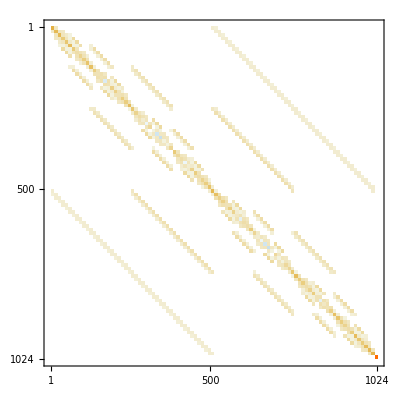

```mathematica
hamiltonianHeisenberg // MatrixPlot
```

## A more interesting example

Let us now turn to a more interesting example: we will consider an Hamiltonian having both single site terms as well as nearest neighbors and next-to-nearest neighbors couplings. It reads (we are assuming here open boundary conditions)

H = h ∑_(i=1)^L σ_i^x - ∑_(i=1)^(L - 1) J_i σ_i^z·(σ_(i+1))^z+ J_2∑_(i=1)^(L - 2) σ_i^z·(σ_(i + 2))^z ≡ H_0 + H_1 + H_2

where the constant h is set to h = 0.6,  J_2 is set to J_2 = 0.3 and the random variables J_i are taken to be J_i = 1 + δJ_i with the variables δJ_i extracted randomly from a uniform distribution with support [-1 , 1].

Let us start by constructing the three terms separately, starting from the easiest, H_0

```mathematica
h = 0.6;
```

```mathematica
couplingsH0 = {Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize}
```

{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}},{{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0}}}

Let us now move to H_1

```mathematica
couplingsH1 = {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]}
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}},{{0,0,-0.957698},{0,0,-1.84172},{0,0,-1.44022},{0,0,-1.38398},{0,0,-1.76864},{0,0,-1.34646},{0,0,-1.24338},{0,0,-0.999613},{0,0,-1.95009}}}

and finally we do the H_2 term

```mathematica
j2 = 0.3; 
couplingsH2 = {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]}
```

{{{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,10}},{{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3}}}

Now that we have all the terms, we can simply join them

```mathematica
couplingsFullH = Join @@@ Transpose @ {couplingsH0 , couplingsH1 , couplingsH2}
```

{{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{1,3},{2,4},{3,5},{4,6},{5,7},{6,8},{7,9},{8,10}},{{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0.6,0,0},{0,0,-0.957698},{0,0,-1.84172},{0,0,-1.44022},{0,0,-1.38398},{0,0,-1.76864},{0,0,-1.34646},{0,0,-1.24338},{0,0,-0.999613},{0,0,-1.95009},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3},{0,0,0.3}}}

and get the final Hamiltonian (as well as its decomposition in terms of unitaries)

```mathematica
{hamiltonianDecomposed , hamiltonianFull} = SpinChainHamiltonian @@ couplingsFullH
```

{{{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]},{SparseArray[…]}},SparseArray[…]}

let us check that all the decomposed terms are proportional to unitary matrices: as a first step let us check if the product of the elements with their conjugate transpose give diagonal matrices

```mathematica
Map[(DiagonalMatrixQ[ConjugateTranspose @ # . #]  &), hamiltonianDecomposed , {2}]
```

{{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True},{True}}

the answer is positive, so it just remains to check that the diagonal elements are all equals to each other. To do this, we tally all the elements of the diagonals and check if the resulting list has length equal to one

```mathematica
Map[(Length @ Tally @ Diagonal[ConjugateTranspose @ # . #]  &), hamiltonianDecomposed , {2}]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

We can also visualize the level of sparsity of the full hamiltonian

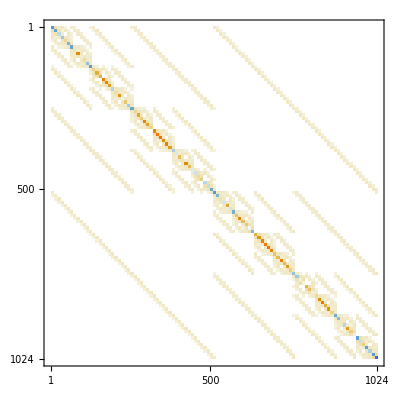

```mathematica
hamiltonianFull // MatrixPlot
```

## More exotic Hamiltonians: SpinOperators function

Whenever one needs to build a more general Hamiltonian, which cannot be built using the function SpinChainHamiltonian or, more generally, if one needs to build explicitly the spin operators, σ_i^a, the function SpinOperators[L] gives the spin operators defined on a spin chain of length L. So, for example

```mathematica
sS = SpinOperators[latticeSize]
```

{{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]},{SparseArray[…],SparseArray[…],SparseArray[…]}}

We see that the spin operators are formatted as a list of lists. Each of the sublists contains the three spin operators defined at a given position in the chain.

## Studying a given Hamiltonian: FindGroundState, EnergyStored and FindBandwidth

Once we have the Hamiltonian, we can now start to study its properties. The first two functions we are going to explore are very simple. As the name suggests, the function FindGroundState[hamiltonian] simply computes the ground state (i.e. the state with the lowest energy) associated to a given Hamiltonian.  As an example, let us consider the non-trivial spin-chain Hamiltonian we introduced in the last example and that we recall quickly here

H = h ∑_(i=1)^L σ_i^x - ∑_(i=1)^(L - 1) J_i σ_i^z·(σ_(i+1))^z+ J_2∑_(i=1)^(L - 2) σ_i^z·(σ_(i + 2))^z ≡ H_0 + H_1 + H_2

```mathematica
h = 0.6;
j2 = 0.3; 
hamiltonian = SpinChainHamiltonian @@ Join @@@ Transpose @ {{Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize} , {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]} , {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]}} // Last;
```

The ground state is then given by

```mathematica
groundState = FindGroundState @ hamiltonian;
```

and, by making use of the function EnergyStored[groundState , hamiltonian] we can compute the associated ground state energy

```mathematica
groundEnergy = EnergyStored[groundState , hamiltonian]
```

-9.95287

Notice that, more generally, the function EnergyStored[state , observable] computes the mean value (in the quantum mechanical sense) of the operator observable in the quantum state state, i.e. it does not assume that state is an eigenstate of observable.

Finally, in many applications in condensed matter physics, one needs to compare different Hamiltonians defined at different energy scales. To make meaningful comparisons, it is often useful to compute the bandwidth of a given Hamiltonian, i.e. to compute the energy difference between the energy of the state with maximum energy and the energy of the ground state. The bandwidth of a given hamiltonian is computed by the function FindBandwidth[hamiltonian].

```mathematica
bandwidth = FindBandwidth @ hamiltonian
```

21.8767

## A quantum algorithm: quantum imaginary time evolution using QITE

We now move to describe a quantum computing algorithm: we will approximate the ground state, denoted by |G⟩, of a given Hamiltonian H, by using the so called “Quantum imaginary time evolution” algorithm (QITE). The imaginary time evolution (ITE) algorithm, is a well known iterative algorithm to efficiently approximate |G⟩ via an iterative procedure starting from an initial ket, denoted by |ψ_0⟩. The main property of the ITE algorithm is that it always converges to |G⟩, provided that the initial Ansatz|ψ_0⟩ had a non vanishing overlap with it. This is a kind of assumption which is pretty easy to satisfy and that, in particular, does not assume any prior good physical understanding of the physical system under investigation, since it just requires that ⟨G|ψ_0⟩ be non-vanishing, a condition which is typically very easy to satisfy.

On the other hand, as we will see the ITE algorithm makes use of non-unitary operators, thus making this algorithm not particularly suitable to be implemented on a quantum computer, especially on a so-called NISQ machine.

In the next section, we will provide a simple introduction to the ITE algorithm and to its quantum version. In the other sections, we will describe how the function QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD , compiled_ : “True” , toleranceNumeric :10^-6 , deltaDiagonal : 0.1] can be used to implement the QITE algorithm on different physical spin chain models.

## The ITE algorithm and its quantum version, a short introduction

In this section we introduce the idea of quantum imaginary time evolution and how it can be modified to make it suitable for a quantum machine. The basic idea is very simple: let us consider an initial state, called |ψ_0⟩. As it is well-known, its time evolution (under the Hamiltonian H which, for simplicity, we assume to be time-independent) is dictated by the Schrödinger equation which, once solved, gives us the time evolved expression for the state

|ψ (t)⟩ = Exp(- i H t)|ψ_0⟩

Where the expression Exp(- i H t) refers to the matrix exponential of the operator - i H t, defined through its Taylor expansion. We can gain a better intuition of the dynamics by the following observation: we can expand the initial ket, |ψ_0⟩, on the basis defined by the eigenstates of H, i.e. on the complete set of states |E^a⟩ satisfying the relations

H |E^a⟩ = E^a|E^a⟩    

with  E^0 < E^1 < E^2 …  being the energies of the system (they are real numbers, given that H is Hermitian). The expansion of|ψ_0⟩ on the eigenstates of H reads

|ψ_0⟩ = ∑_(a=0)^(dim H) c_0^a |E^a⟩

and, in terms of this decomposition, the time evolution can be easily computed explicitly. One simply gets

|ψ(t)⟩ = ∑_(a=0)^(dim H) (c_0^a e^(- i E^a t)) |E^a⟩ .

from which we see that, by time evolution, the coefficients c_0^a of the expansion are simply multiplied by the factors e^(- i E^a t). The crucial observation is now the following: given that the energies E^a are all real numbers, it follows that the modulus  of the various coefficients c_0^a  is unchanged by time evolution, i.e.

|c_0^a e^(- i E^a t)| = |c_0^a| .

The situation is completely different if we assume that t is an imaginary, rather than real, number. Let us denote with β  the real number defined by β ≡ i t . Under this assumption we get  for the imaginary time evolved state 

|ψ(β)⟩ = ∑_(a=0)^(dim H) (c_0^a e^(- E^a β)) |E^a⟩

and, this time, the modulus of the coefficients c_0^a decreases by time evolution

|c_0^a e^(- E^a β)| < |c_0^a|

and, in particular, we see that the coefficients are more and more suppressed when a increases. Putting the things together we see

|ψ(β)⟩  ∝ |E^min⟩  for large enough values of β

Here, we denoted by|E^min⟩ the eigenstate of  H with the smallest energy, such that the corresponding expansion coefficient, c_0^min is non vanishing. In particular, if c_0^0 ≠ 0, we see that for large enough β the imaginary time evolved ket|ψ(β)⟩ converges to the ground state

|ψ(β)⟩  ∝ |E^0⟩  .

After this preliminaries, we are now convinced that an efficient method to find the ground state of a given system is to perform the imaginary time evolution

|ψ (β)⟩ = Exp(-  H β)|ψ_0⟩

for large enough β. However, we immediate recognize two  problems. The first one is in common to the real time evolution equation

|ψ (t)⟩ = Exp(- i H t)|ψ_0⟩

and is simply that the unitary operator Exp(- i H t) is hard to implement with simple circuits. A possible way out to this problem is offered by the so-called Suzuki-Trotter algorithm: suppose, as it is often the case, that our Hamiltonian operator H is k-local, i.e., it is given by the sum of terms h[m], each of them acting on k qubits at most

H = ∑_(m=1)^M h[m]

In such a case, the time evolution operator  Exp(- i H t) can be effectively replaced, up to small errors, by the following expression

|ψ (t)⟩ = Exp(- i H t)|ψ_0⟩ ∼ (∏_(m = 1)^M Exp(- i h[m] Δt))^n |ψ_0⟩           with n = t/Δt

up to an error of order O(Δt). The main advantage is that the single unitary operators Exp(- i h[m] Δt) are now acting on few qubits and they can be more easily implemented on a quantum computer. Turning to the imaginary time setup, we realize that the ground state can be obtained by the following, imaginary time, Suzuki-Trotter algorithm: 

|ψ (β)⟩ = Exp(-  H β)|ψ_0⟩ ∼ (∏_(m = 1)^M Exp(-  h[m] Δτ))^n |ψ_0⟩           with n = β/Δτ

However, we need now to face another difficulty: the operators Exp(-  h[m] Δτ) are not unitary operators, and so they cannot be naturally implemented by a quantum computer.
A way to solve this problem is the following:  the non-unitary, rescaled, operator action

c^(-1/2) *Exp(-  h[m] Δτ) |ψ⟩       with      c ≡ ⟨ψ|Exp(- 2 h[m] Δτ)|ψ⟩ 

can be effectively mimicked by a unitary operator action

c^(-1/2) *Exp(-  h[m] Δτ) |ψ⟩ ∼ Exp(- i  A[m] Δτ) |ψ⟩

where the Hermitian operator A[m]  acts on a domain which is larger than the domain of  the original operator, h[m]. The unitary approximation becomes more and more efficient by increasing the dimension of the domain of A[m] or by reducing the correlation length of |ψ⟩.

The function QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD , compiled_ : “True” , toleranceNumeric :10^-6 , deltaDiagonal : 0.1] performs the QITE algorithm just outlined. It receives as inputs the lattice size of the spin chain, the Suzuki-Trotter decomposition of the Hamiltonian and, in correspondence of this decomposition, it needs also the list of the lattice sites where the single terms, h[m]. Moreover, it needs to know also the maximum imaginary time to simulate, β, the single time step, Δt, the initial state, initialState and, finally, how bigger the domain of A[m] should be with respect to the domain of h[m].

In the next two sections, we will consider two examples of usage.

## Finding the ground state using QITE: the Heisenberg model example

As the simplest example, let us consider the Heisenberg Hamiltonian

H_Heis = ∑_(i j) ∑_(a=1)^3 σ_i^a · σ_j^a

As usual, we first construct the graph of the non vanishing couplings and the corresponding Hamiltonian

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1];
{hamiltonianDecomposed , hamiltonian} = SpinChainHamiltonian[listCouplings , ({1 , 1 , 1} &) /@ Range @ Length @ listCouplings];
```

And, once again, we compute the ground state and its energy

```mathematica
groundStateHeisenberg = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergyHeisenberg = EnergyStored[groundStateHeisenberg , hamiltonian]
```

-18.0618

We now set the values of β , Δτ and the initial ket |ψ_0⟩

```mathematica
β = 3.;
Δt = 0.1;
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
```

Finally,we consider two cases for the domains of A[m], dD = 0 which corresponds to the case in which A[m]  has the same support of h[m]; and dD = 1 which corresponds to the case in which the domain of A[m] includes an extra qubits, both at the left and at the right of h[m].

```mathematica
dD = {0 , 1};
```

we now compute the evolved ket using the QITE algorithm

```mathematica
evolvedKetHeisenberg = Parallelize[(QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , #] &) /@ dD]
```

{{{0.,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,621,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},30},1}
 |  |  |  |

As usual, the evolved ket is given as a list of lists, with each sublists having two elements: the first is the imaginary time, the second is the ket itself.

We can compute the mean energy stored in the evolved ket.

```mathematica
energyHeisenberg = Apply[({#1 , Conjugate @ #2 . hamiltonian . #2} &) , evolvedKetHeisenberg , {2}] ;
```

which we plot

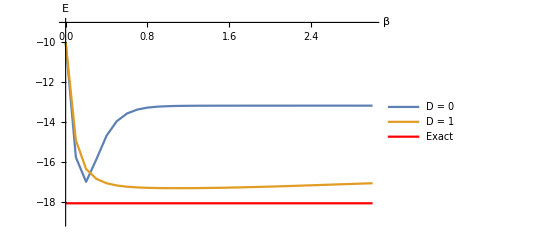

```mathematica
Show[ListPlot[energyHeisenberg , Joined->True , PlotRange->{All , {-9 , -19}} , PlotLegends -> {"D = 0" , "D = 1"} , AxesLabel -> {"β" , "E"}] , Plot[groundEnergyHeisenberg , {x , 0 , 3} , PlotStyle-> Red , PlotLegends->{"Exact"} , PlotRange -> All]]
```

We see that, while at dD = 0 the approximation is not very efficient, things change quite a lot at dD = 1, with a good approximation of the mean energy.

## Finding the ground state using QITE: a more interesting example

We can now perform exactly the same analysis for the more interesting model

H = h ∑_(i=1)^L σ_i^x - ∑_(i=1)^(L - 1) J_i σ_i^z·(σ_(i+1))^z+ J_2∑_(i=1)^(L - 2) σ_i^z·(σ_(i + 2))^z ≡ H_0 + H_1 + H_2

where the constant h is set to h = 0.6,  J_2 is set to J_2 = 0.3 and the random variables J_i are taken to be J_i = 1 + δJ_i with the variables δJ_i extracted randomly from a uniform distribution with support [-1 , 1];

```mathematica
h = 0.6;
couplingsH0 = {Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize};
couplingsH1 = {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]};
j2 = 0.3; 
couplingsH2 = {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]};
couplingsFullH = Join @@@ Transpose @ {couplingsH0 , couplingsH1 , couplingsH2};
```

```mathematica
listCouplings = First @ couplingsFullH;
{hamiltonianDecomposed , hamiltonian} = SpinChainHamiltonian @@ couplingsFullH;
```

As before, we compute the actual ground state and the corresponding energy

```mathematica
groundState = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergy = EnergyStored[groundState , hamiltonian]
```

-8.34691

and, once again, we set the parameters of the simulation

```mathematica
β = 3.;
Δt = 0.1;
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
dD = {0 , 1};
```

we compute the QITE algorithm

```mathematica
evolvedKet= Parallelize[(QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , #] &) /@ dD];
```

the associated mean energy stored

```mathematica
energy = Apply[({#1 ,Conjugate @ #2 . hamiltonian . #2} &) , evolvedKet , {2}] ;
```

which we plot

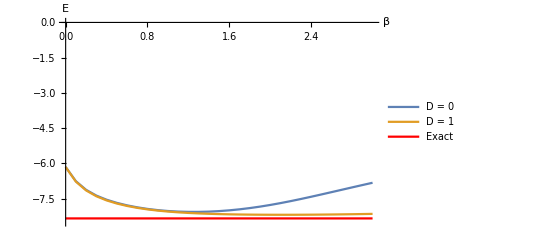

```mathematica
Show[ListPlot[energy, Joined->True , PlotRange->{All , {0. , 1.2}} , PlotLegends -> {"D = 0" , "D = 1"} , AxesLabel -> {"β" , "E"}] , Plot[1 , {x , 0 , 3} , PlotStyle-> Red , PlotLegends->{"Exact"}]]
```

Once again, we see that by just taking dD = 1 the quality of the approximation is very good.

## Studying time evolution via EvolvedStateList

As already discussed in the previous chapter, once a ket, |ψ_0⟩ is given, the time evolution of the same ket under a given time independent Hamiltonian, H, is controlled by the Schrödinger equation, whose solution is 

|ψ (t)⟩ = Exp(- i H t)|ψ_0⟩

The function EvolvedStateList[stateIn , hamiltonian , tMin , tMax , nPoints] gives the result of the time evolution, computed in the time interval [tMin , tMax] with nPoints intermediate steps, equally spaced in time. Optionally, the function EvolvedStateList[stateIn , hamiltonian , tMin , tMax , nPoints , “Log”] does the same thing, but this time the discrete points are equally spaced in Log_10 scale.

Let us consider an example. As the initial ket |ψ_0⟩ we take the ground state of the Hamiltonian

H_0 = h ∑_(i=1)^L σ_i^x

with h = 0.6

This can be done using the functions already introduced: we first construct H_0

```mathematica
h = 0.6;
h0 = SpinChainHamiltonian @@{Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize} // Last;
```

and then we compute its ground state

```mathematica
stateIn = FindGroundState @ h0;
```

whose energy can be easily computed

```mathematica
initialEnergy = EnergyStored[stateIn , h0]
```

-6.

Let us now assume that we want to study the time evolution of stateIn under the following quench Hamiltonian (already introduced in a previous section)

H =H_0 - ∑_(i=1)^(L - 1) J_i σ_i^z·(σ_(i+1))^z+ J_2∑_(i=1)^(L - 2) σ_i^z·(σ_(i + 2))^z

the quench Hamiltonian is constructed in the following way

```mathematica
j2 = 0.3; 
hamiltonian = SpinChainHamiltonian @@ Join @@@ Transpose @ {{Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize} , {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]} , {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]}} // Last;
```

We can now compute the time evolved ket in the time interval, say [0.01 , 1000], with 1000 intermediate points, equally spaced in Log_10 scale.

```mathematica
tMin = 0.01;
tMax = 1000;
nPoints = 1000;
evolvedKetList = EvolvedStateList[stateIn , hamiltonian , tMin , tMax , nPoints , "Log"];
```

As we can see, the result of EvolvedStateList is a list of lists. Each of the nested lists has two elements: the first is the time at which the evolved ket is computed, the second is the evolved ket itself.

As an application, we can compute the averaged energy, as measured by H_0, stored in the evolved ket |ψ(t)⟩, 

E(t) = ⟨ψ(t)| H_0 | ψ(t)⟩ - ⟨ψ_0| H_0 | ψ_0⟩

```mathematica
energyList = evolvedKetList /. {{x_ , y_} -> {x , EnergyStored[y , h0] - initialEnergy}} // Chop;
```

which we can plot

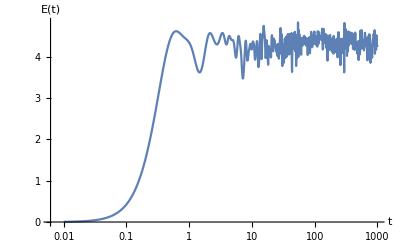

```mathematica
ListLogLinearPlot[energyList , Joined -> True , PlotRange -> All , AxesLabel -> {"t" , "E(t)"}]
```

we see that, after an initial rise (due to the fact that, by time evolution, the highly excited states of H_0 get involved in the expansion of |ψ(t)⟩) the mean energy stored in the evolved ket, E(t), fluctuates erratically.

## Entanglement measures via PartialTrace and EntanglementEntropy

Given a pure state |ψ⟩, defined over a lattice G, one is often interested in studying its entanglement properties under bi-partitions of the lattice. The typical example is the following: suppose that the lattice G is made of 10 sites, we would like to consider a bi-partition of the lattice in two sub-lattices, A and B, each of them composed by 5 sites. We will say that |ψ⟩ is un-entangled if it can be written as the tensor product of two states, (|ψ⟩)_A and (|ψ⟩)_B, defined over the sub-lattices A and B, respectively, i.e.

((|ψ⟩ = |ψ⟩)_A ⊗ |ψ⟩)_B 

If such a rewriting is not possible, the state is said entangled.

The level of entanglement can be measured via the Entanglement entropy: the entanglement entropy of |ψ⟩, under the bi-partition of the lattice G in A and B, is measured by doing a partial trace of |ψ⟩, over the degrees of freedom defined on the B system, and getting the density matrix ρ

ρ ≡ Tr_B (|ψ⟩ ⟨ψ|)

once the density matrix ρ is obtained, the entanglement entropy is simply computed by the formula

S(ρ) ≡ - Tr_A (ρ Log_2 ρ)

From what we wrote, we understand that the problem of computing the entanglement entropy, under a bi-partition of the lattice, of a given pure state |ψ⟩ can be splitted in two pieces: first we need to compute the partial trace over the B degrees of freedom, and then we compute the entanglement entropy of the resulting density matrix. The first step can be done with the function PartialTrace[stateIn , tracedSites , nSites] which receives as input the initial ket, |ψ⟩ , the list of sites over which we want to perform the partial trace, i.e., the lattice sites defining the B sub-system, and the total number of sites which compose the full lattice G. As a result, PartialTrace gives back the density matrix ρ. The entanglement entropy can then be computed by means of the function EntanglementEntropy[densityMatrix].

As an example, let us consider the time evolution of the entanglement entropy under the time evolution dynamics introduced in the previous section: the evolved ket is computed using the method of the previous section

```mathematica
h = 0.6;
h0 = SpinChainHamiltonian @@{Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize} // Last;
stateIn = FindGroundState @ h0;
j2 = 0.3; 
hamiltonian = SpinChainHamiltonian @@ Join @@@ Transpose @ {{Partition[Range @ latticeSize , 1] , ({h , 0 , 0} &) /@ Range @ latticeSize} , {Partition[Range @ latticeSize ,2 , 1] , ({0 , 0 , - (1 + RandomReal[{-1 , 1}])} &) /@ Range @ Length @ Partition[Range @ latticeSize ,2 , 1]} , {({# , # + 2} &)/@ Range[latticeSize - 2] , ({0 , 0 , j2} &) /@ Range @ Length @ Range[latticeSize - 2]}} // Last;
tMin = 0.01;
tMax = 1000;
nPoints = 1000;
evolvedKetList = EvolvedStateList[stateIn , hamiltonian , tMin , tMax , nPoints , "Log"];
```

Having obtained the time evolved ket, we can assume we want to compute the entanglement entropy associated by a bi-partition of the lattice in two sub-lattices, in which we trace over the first  half of the qubits. This is simply done

```mathematica
entanglementEntropy = evolvedKetList /. {{x_ , y_} :> {x , EntanglementEntropy @ PartialTrace[y , Range[latticeSize / 2] , latticeSize]}};
```

Which we can plot as a function of the time

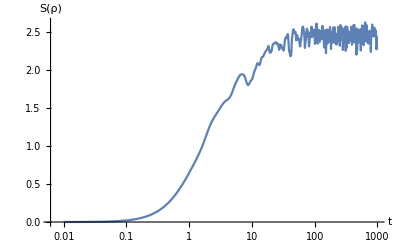

```mathematica
ListLogLinearPlot[entanglementEntropy , Joined -> True , PlotRange -> All , AxesLabel -> {"t" , "S(ρ)"}]
```

## Creating Majorana fermions and SYK Hamiltonians using GammaMatrices and SYKHamiltonian

The package contains also some functionalities to generate Majorana fermions operators. Let us recall that Majorana fermions operators are simply quantum operators, denoted by γ^i with i = 1, … , N≡ 2L satisfying the following anti-commutation relations

{γ^i , γ^j} = 2 δ^ij

It is well-known that they can be considered as highly non-local operators defined on a spin-chain lattice of length L, via the following map (usually called Jordan-Wigner Map)

γ^(2 j - 1) = (∏_(i = 1)^(j - 1) σ_i^z) σ_j^x                      γ^(2 j) = (∏_(i = 1)^(j - 1) σ_i^z) σ_j^y

The sparse matrices corresponding to the Jordan-Wigner map just reported can be obtained by the function GammaMatrices[L] which returns the 2L corresponding Majorana operators

For example

```mathematica
gammaMatrices = GammaMatrices[latticeSize]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

A particular Hamiltonian, built out of the Majorana operators just introduced, which is attracting a considerable amount of attention in recent days, is the so-called SYK_q Hamiltonian, which is written as 

H_q≡ (i/2)^(q / 2) ∑_(i < j < k < l) J_ijkl γ^i γ^j γ^k γ^l

where the coupling constants J_ijkl are extracted randomly from a Gaussian distribution, having mean value 0 and variance

⟨ J_ijkl^2⟩ ≡ ((q - 1)!)/N^(q - 1)

The function SYKHamiltonian[q , nGamma , gamma] builds the SYK_q Hamiltonian, for a total of nGamma Majorana operators, represented by the operators gamma.

For example

```mathematica
hamiltonian = SYKHamiltonian[4 , 2 * latticeSize , gammaMatrices]
```

SparseArray[<262144>, {1024, 1024}]

which can be visualized using MatrixPlot

```mathematica
hamiltonian // MatrixPlot
```

-Graphics-

Of course, the vast majority of the functions we defined in the previous Chapters can be used for the SYK Hamiltonian too; the only exception, for the moment, being the function QITE.